# Visualisation Figure

Ruvi Lecamwasam, ruvi.lecamwasam@anu.edu.au

## Import Data

```mathematica
SetDirectory@NotebookDirectory[];

phasespacecsv=Import["phasespace.csv"];
end=3000;
t=phasespacecsv[[;;end,1]];
x=phasespacecsv[[;;end,2]];
px=phasespacecsv[[;;end,3]];
a2=phasespacecsv[[;;end,4]];
v=phasespacecsv[[;;end,5]];
Print["phasespace fullsys.csv"];
```

phasespace fullsys.csv

```mathematica
Length[t]
```

3000

## Generate figures

### Fig 4a Output trace from levitating mirror

```mathematica
labelStyle=Directive[FontSize->25,FontColor->Black];
plotOpts=Sequence[ImageSize->Large,LabelStyle->labelStyle,AxesLabel->{"τ̃",}];
```

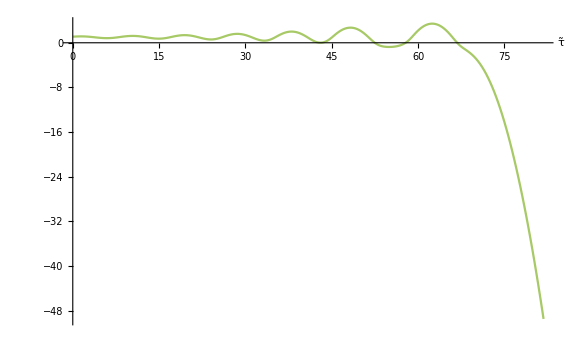

```mathematica
tracePlot=ListLinePlot[Transpose@{t,x},plotOpts,PlotRange->All,ColorFunction->Function[{x,y},ColorData["BlueGreenYellow"][x]]]
```

```mathematica
SetDirectory@NotebookDirectory[];
Export["figVisualisation_Trace.png",tracePlot];
```

### Fig 4b Motion in potential

```mathematica
traj=Interpolation[{#[[1]],{#[[2]],#[[3]],#[[4]]}}&/@Transpose[{t,t,x,v}]];
```

```mathematica
labelStyle=Directive[FontSize->30,FontColor->Black,FontFamily->"Times New Roman"];
trajPlot=ParametricPlot3D[traj[τ],{τ,t[[1]],t[[-1]]},ImageSize->Large,LabelStyle->labelStyle,AxesLabel->{"τ̃","x̃","Ṽ"},BoxRatios->{1.5,1,0.5},ColorFunction->Function[{x,y,z,t},ColorData["BlueGreenYellow"][t]],PlotRange->{All,{-5,3.7},Automatic},Ticks->{Automatic,Automatic,{-1,-0.5,0}}];
potential=Plot3D[0.5 x-ArcTan[x],{τ,t[[1]],t[[-1]]},{x,-5,3.7},PlotStyle->{LightBlue,Opacity[0.2]},Mesh->None];
potentialPlot=Show[trajPlot,potential]
```

-Graphics3D-

```mathematica
SetDirectory@NotebookDirectory[];
Export["figVisualisation_Potential.pdf",potentialPlot];
```

### Fig 4c Adiabatic manifold

```mathematica
traj=Interpolation[{#[[1]],{#[[2]],#[[3]],#[[4]]}}&/@Transpose[{t,x,px,a2}]];
```

```mathematica
trajPlot=ParametricPlot3D[traj[τ],{τ,t[[1]],t[[-1]]},ImageSize->Large,LabelStyle->labelStyle,AxesLabel->{"x̃","(p̃)_x","|α̃|^2"},BoxRatios->{1.5,1,1},ColorFunction->Function[{x,y,z,t},ColorData["BlueGreenYellow"][t]],PlotRange->{{-5,4},{-2,2},All}];
manifold=Plot3D[1/(1+x^2),{x,-5,4},{y,-2,2},PlotStyle->{LightOrange,Opacity[0.2]},Mesh->None,MaxRecursion->5];
adiabaticPlot=Show[trajPlot,manifold]
```

-Graphics3D-

```mathematica
SetDirectory@NotebookDirectory[];
Export["figVisualisation_Adiabatic.pdf",adiabaticPlot];
```